```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

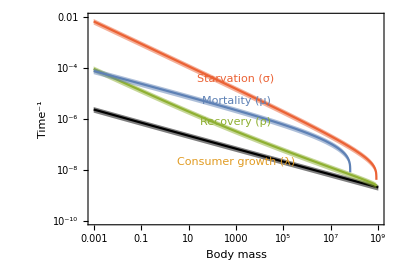

```mathematica
RatePlot=Show[{
Error=0.25;
LogLogPlot[{
ConsumerGrowth,
ConsumerGrowth*(1+Error),
ConsumerGrowth*(1-Error)},{M,0.001,10^9},PlotStyle->{Black,Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[{Black,Opacity[0.5]}],
Frame->True,FrameLabel->{"Body mass","Time^-1"},PlotRange->{10^-10,10^-2}],
LogLogPlot[{
Starvation,
Starvation*(1+Error),
Starvation*(1-Error)},{M,0.001,10^9},PlotStyle->{ColorData[97,4],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[{ColorData[97,4],Opacity[0.5]}]],
LogLogPlot[{
Recovery,
Recovery*(1+Error),
Recovery*(1-Error)},{M,0.001,10^9},PlotStyle->{ColorData[97,3],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[{ColorData[97,3],Opacity[0.5]}]],
LogLogPlot[{
Mortality,
Mortality*(1+Error),
Mortality*(1-Error)},{M,0.001,10^9},PlotStyle->{ColorData[97,1],Transparent,Transparent},Filling->{2->{3}},FillingStyle->Directive[{ColorData[97,1],Opacity[0.5]}]],

Graphics[Rotate[Text[Style["Mortality (μ)",FontColor->ColorData[97,1]],{Log@1000,Log@(10^-5.3)}],345Degree]],
Graphics[Rotate[Text[Style["Starvation (σ)",FontColor->ColorData[97,4]],{Log@1000,Log@(10^-4.4)}],335Degree]],
Graphics[Rotate[Text[Style["Recovery (ρ)",FontColor->ColorData[97,3]],{Log@1000,Log@(10^-6.1)}],340Degree]],
Graphics[Rotate[Text[Style["Consumer growth (λ)",FontColor->ColorData[97,2]],{Log@1000,Log@(10^-7.7)}],347Degree]]
},AspectRatio->Automatic]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_Rates.pdf"}],RatePlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_Rates.pdf